```mathematica
Get["C:\\Users\\rutar\\OneDrive\\Desktop\\Domača_naloga_2\\MonteCfunkcija.m"]
```

```mathematica
MonteCarloπ[n_]:=Module[{vrednosti},vrednosti=Table[MonteC[i],{i,1,n}];
ListLinePlot[vrednosti,AxesLabel->{"Število poskusov n","Vrednost π"},PlotRange->{0,4.5}]];
```

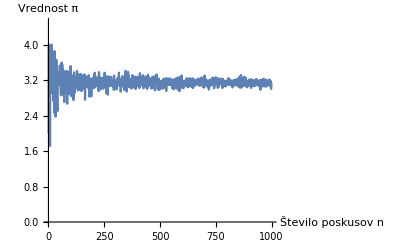

```mathematica
MonteCarloπ[1000]
```

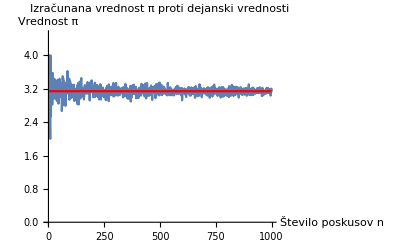

```mathematica
Show[MonteCarloπ[1000],Plot[π,{n,0,1000},PlotStyle->Red],PlotLabel->"Izračunana vrednost π proti dejanski vrednosti"]
```